```mathematica
rawdataH=
Import[NotebookDirectory[]<>"1110_H.csv"];
sinalH=Transpose[rawdataH][[5]];
rawdataV=
Import[NotebookDirectory[]<>"1110_V.csv"];
sinalV=Transpose[rawdataV][[5]];
```

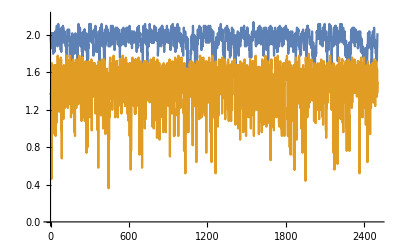

```mathematica
ListLinePlot[{sinalH,sinalV},PlotRange->{0,2.2}]
```

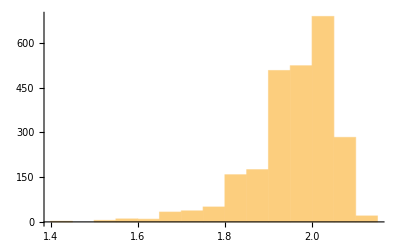

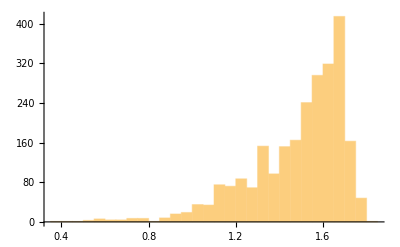

```mathematica
Histogram[sinalH]
Histogram[sinalV]
```